```mathematica
SetDirectory["C:\\Users\\sterg\\Documents\\GitHub\\sparks-baird\\bayes-opt-particle-packing"]
```

C:\Users\sterg\Documents\GitHub\sparks-baird\bayes-opt-particle-packing

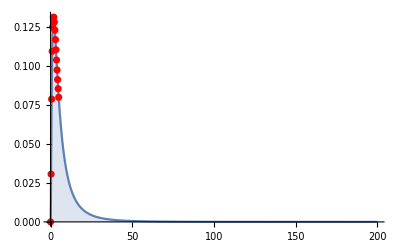

```mathematica
dist=LogNormalDistribution[Log@5,1];
pts=Subdivide[0,5,15];
p1=Plot[PDF[dist,x],{x,0,200},PlotRange->Full,Filling->Axis];
p2=ListPlot[{pts,PDF[dist,pts]}ᵀ,PlotStyle->Red];
Show[p1,p2]
```

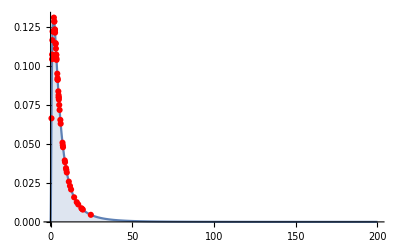

```mathematica
dist=LogNormalDistribution[Log@5,1];
p1=Plot[PDF[dist,x],{x,0,200},PlotRange->Full,Filling->Axis];
pts=RandomVariate[dist,50];
p2=ListPlot[{pts,PDF[dist,pts]}ᵀ,PlotStyle->Red];
Show[p1,p2]
```

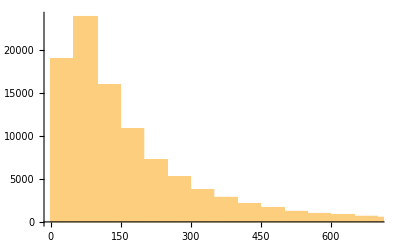

197.615

```mathematica
Histogram@RandomVariate[dist,100000]
Mean@RandomVariate[dist,100000]
```

```mathematica
PDF[dist,RandomVariate[dist]]
```

9.85645×10^-54

```mathematica
q=Quantile[dist,0.5]
```

2.71828

```mathematica
dist2=LogNormalDistribution[μ,σ];
```

```mathematica
<<Notation`
```

```mathematica
Symbolize[Subscript[_, _]]
```

```mathematica
soln=Solve[{Subscript[μ, 2]==Mean@dist2,Subscript[σ, 2]==StandardDeviation@dist2},{μ,σ},]⟦1⟧//FullSimplify
```

{μ→ConditionalExpression[Log[μ_2]-1/2 Log[1+σ_2^2/μ_2^2], 0<σ_2<μ_2 √(-1+μ_2^2)],σ→ConditionalExpression[√Log[1+σ_2^2/μ_2^2], 0<σ_2<μ_2 √(-1+μ_2^2)]}

```mathematica
soln⟦1⟧
```

μ→ConditionalExpression[Log[μ_2]-1/2 Log[1+σ_2^2/μ_2^2], 0<σ_2<μ_2 √(-1+μ_2^2)]

```mathematica
<<ToMatlab`
```

```mathematica
Subscript[eqn, μ]=μ/.soln/.{Subscript[μ, 2]->mu,Subscript[σ, 2]->sigma}//Normal;
Subscript[eqn, σ]=σ/.soln/.{Subscript[μ, 2]->mu,Subscript[σ, 2]->sigma}//Normal;
ToMatlab[Subscript[eqn, μ]]
ToMatlab[Subscript[eqn, σ]]
```

log(mu)+(-1/2).*log(1+mu.^(-2).*sigma.^2);

log(1+mu.^(-2).*sigma.^2).^(1/2);

```mathematica
"2.*log(mu)+(-1/2).*log(mu.^2+sigma);\\n
```

```mathematica
FortranForm[eqn]
```

2*Log(mu) - Log(mu**2 + sigma)/2.

```mathematica
Dist[μ_,σ_]:=LogNormalDistribution[Log@μ,σ]
MyPDF[μ_,σ_,n_:1000]:=Module[{}, 
dist=Dist[μ,σ];
samples=RandomVariate[dist,n]
(*PDF[dist,samples]*)
(*cutoff=Quantile[dist,0.95];*)
(*Select[pdf,#<5000&]*)
]
{Subscript[μ, min],Subscript[μ, max]}={1,5};
{Subscript[σ, min],Subscript[σ, max]}={0.1,1};
n=5;
dμ=(Subscript[μ, max]-Subscript[μ, min])/(n-1);
dσ=(Subscript[σ, max]-Subscript[σ, min])/(n-1);
```

```mathematica
params=Table[{μ,σ},{μ,Subscript[μ, min],Subscript[μ, max],dμ},{σ,Subscript[σ, min],Subscript[σ, max],dσ}];
```

```mathematica
(*data=Table[MyPDF[μ,σ,1000],{μ,Subscript[μ, min],Subscript[μ, max],dμ},{σ,Subscript[σ, min],Subscript[σ, max],dσ}];
Histogram[Flatten[data,1],50,ChartLayout->{"Column",5},ScalingFunctions->{Automatic,"Log"}]*)
```

```mathematica
MyHistogram[μ_,σ_,n_:1000]:=Module[{data},
dist=Dist[μ,σ];
data=RandomVariate[dist,n];
mx=Round[Quantile[data,0.99],0.01];
Histogram[data,PlotRange->{{0,mx},Automatic},Ticks->{{0,mx},Automatic},AspectRatio->1,ImageSize->120,PlotRangeClipping->False]
]
hists=Table[MyHistogram[μ,σ,100000],{μ,Subscript[μ, min],Subscript[μ, max],dμ},{σ,Subscript[σ, min],Subscript[σ, max],dσ}];
```

```mathematica
histTbl=TableForm[hists,TableHeadings->{"μ="~StringJoin~ToString@#&/@N@Range[Subscript[μ, min],Subscript[μ, max],dμ],"σ="~StringJoin~ToString@#&/@N@Range[Subscript[σ, min],Subscript[σ, max],dσ]},TableAlignments->Center]
```

| σ=0.1 | σ=0.325 | σ=0.55 | σ=0.775 | σ=1.
μ=1. | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
μ=2. | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
μ=3. | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
μ=4. | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
μ=5. | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Export[FileNameJoin[{"figures","mma-size-invariance.png"}],histTbl]
```

figures\mma-size-invariance.png

```mathematica
SystemOpen["figures\\mma-size-invariance.png"]
```

```mathematica
(*ResourceFunction["PlotGrid"][*)
```

```mathematica
(*TableForm[{{TableForm[Table[LogLinearPlot[PDF[Dist[μ,σ],x],{x,1,1100},PlotRange->Full,TicksStyle->Small],{μ,Subscript[μ, min],Subscript[μ, max],dμ},{σ,Subscript[σ, min],Subscript[σ, max],dσ}],TableHeadings->{N@Range[Subscript[μ, min],Subscript[μ, max],dμ],N@Range[Subscript[σ, min],Subscript[σ, max],dσ]},TableAlignments->Center]}},TableHeadings->{{Style["μ",FontSize->24]},{Style["σ",FontSize->24]}},TableAlignments->Center]*)
```

```mathematica
(*TableForm[Table[LogLinearPlot[PDF[Dist[μ,σ],x],{x,1,1100},PlotRange->Full,TicksStyle->Small],{μ,Subscript[μ, min],Subscript[μ, max],dμ},{σ,Subscript[σ, min],Subscript[σ, max],dσ}],TableHeadings->{"μ="~StringJoin~ToString@#&/@N@Range[Subscript[μ, min],Subscript[μ, max],dμ],"σ="~StringJoin~ToString@#&/@N@Range[Subscript[σ, min],Subscript[σ, max],dσ]},TableAlignments->Center]*)
```

```mathematica
tbl=TableForm[Table[Plot[PDF[Dist[μ,σ],x],{x,0,100},PlotRange->Full,TicksStyle->Small,Filling->Axis,AspectRatio->1,ImageSize->120],{μ,Subscript[μ, min],Subscript[μ, max],dμ},{σ,Subscript[σ, min],Subscript[σ, max],dσ}],TableHeadings->{"μ="~StringJoin~ToString@#&/@N@Range[Subscript[μ, min],Subscript[μ, max],dμ],"σ="~StringJoin~ToString@#&/@N@Range[Subscript[σ, min],Subscript[σ, max],dσ]},TableAlignments->Center]
```

| σ=0.1 | σ=0.325 | σ=0.55 | σ=0.775 | σ=1.
μ=1. | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
μ=2. | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
μ=3. | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
μ=4. | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
μ=5. | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Export[FileNameJoin[{"figures","log-normal.png"}],tbl]
```

figures\log-normal.png

If I have two distributions overlaid, does the same behavior with per-sigma results looking identical after scaling hold? Related to the size reparameterization.

```mathematica
MyHistogram2[μ_,σ_,n_:1000]:=Module[{data,data2,datafull},
dist=Dist[μ,σ];
dist2=Dist[2μ,0.5σ];
data=RandomVariate[dist,n];
data2=RandomVariate[dist2,n];
datafull=data~Join~data2;
mx=Round[Quantile[datafull,0.99],0.01];
Histogram[datafull,PlotRange->{{0,mx},Automatic},Ticks->{{0,mx},Automatic},AspectRatio->1,ImageSize->120,PlotRangeClipping->False]
]
```

```mathematica
hists2=Table[MyHistogram2[μ,σ,100000],{μ,Subscript[μ, min],Subscript[μ, max],dμ},{σ,Subscript[σ, min],Subscript[σ, max],dσ}];
```

```mathematica
histTbl2=TableForm[hists2,TableHeadings->{"μ="~StringJoin~ToString@#&/@N@Range[Subscript[μ, min],Subscript[μ, max],dμ],"σ="~StringJoin~ToString@#&/@N@Range[Subscript[σ, min],Subscript[σ, max],dσ]},TableAlignments->Center]
```

| σ=0.1 | σ=0.325 | σ=0.55 | σ=0.775 | σ=1.
μ=1. | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
μ=2. | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
μ=3. | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
μ=4. | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
μ=5. | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Export[FileNameJoin[{"figures","mma-size-invariance-twodist.png"}],histTbl2]
```

figures\mma-size-invariance-twodist.png